```mathematica
Select[Keys[allGraphs4],IsomorphicGraphQ[VertexAdd[CompleteGraph[3],4],allGraphs4[#,"graph"]]&]
```

{333,273,109,13}

```mathematica
allGraphs4[333,"graph"]
```

-Graphics-

```mathematica
allGraphs4[333,"parents"]
```

{324,252,90}

```mathematica
Table[Labeled[allGraphs4[k,"graph"],k],{k,allGraphs4[365,"parents"]}]
```

{-Graphics-363,-Graphics-360,-Graphics-354,-Graphics-353,-Graphics-353,-Graphics-336,-Graphics-333,-Graphics-327,-Graphics-282,-Graphics-279,-Graphics-273,-Graphics-257,-Graphics-257,-Graphics-122}

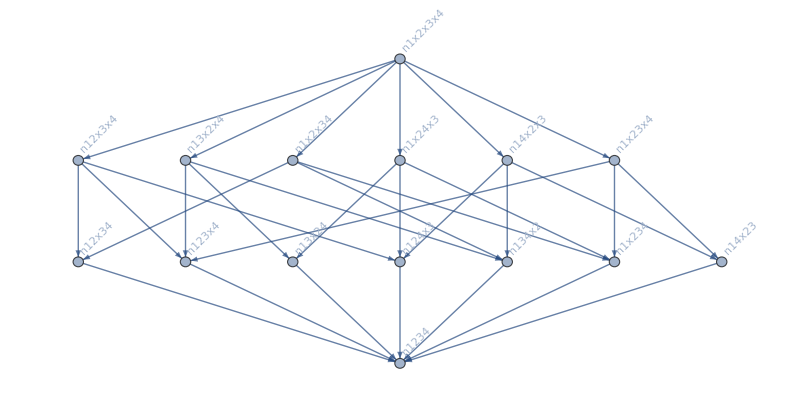
-Graphics-→2 n1x234x5-n1x23x4x5-n1x24x3x5-n1x2x34x5+n1x2x3x4x5
-Graphics-3332 x^2-3 x^3+x^41→0
2→0
3→18
4→96
5→300
6→720
7→1470
-Graphics-→-2 n1x2345+2 n1x234x5+n1x235x4-n1x23x4x5+n1x245x3-n1x24x3x5+n1x25x34-n1x25x3x4-n1x2x34x5+n1x2x3x4x5
-Graphics-360-2 x+5 x^2-4 x^3+x^41→0
2→0
3→12
4→72
5→240
6→600
7→1260
-Graphics-→2 n1x2345-n1x235x4-n1x245x3-n1x25x34+n1x25x3x4
-Graphics-3912 x-3 x^2+x^31→0
2→0
3→6
4→24
5→60
6→120
7→210
-Graphics-→-2 n1x2345+2 n1x234x5+n1x235x4-n1x23x4x5+n1x24x35-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x35x4+n1x2x3x4x5
-Graphics-336-2 x+5 x^2-4 x^3+x^41→0
2→0
3→12
4→72
5→240
6→600
7→1260
-Graphics-→2 n1x2345-n1x235x4-n1x24x35-n1x2x345+n1x2x35x4
-Graphics-3672 x-3 x^2+x^31→0
2→0
3→6
4→24
5→60
6→120
7→210
-Graphics-→-2 n1x2345+2 n1x234x5+n1x23x45-n1x23x4x5+n1x245x3-n1x24x3x5+n1x2x345-n1x2x34x5-n1x2x3x45+n1x2x3x4x5
-Graphics-334-2 x+5 x^2-4 x^3+x^41→0
2→0
3→12
4→72
5→240
6→600
7→1260
-Graphics-→2 n1x2345-n1x23x45-n1x245x3-n1x2x345+n1x2x3x45
-Graphics-3652 x-3 x^2+x^31→0
2→0
3→6
4→24
5→60
6→120
7→210

```mathematica
TableForm[With[{full=MobiusGraph4[K4Key,allGraphs4]},
Table[
Framed[
allGraphs5[k,"graph"]->
With[{sub2=MobiusGraph4[k,allGraphs4]},
Column[{
allGraphs5[k,"colofourrealnull"],

Labeled[
Graph[EdgeList[full],GraphHighlight->Join[EdgeList[sub2],VertexList[sub2]],ImageSize->800, 
VertexLabels->Table[n->Rotate[(TableForm[n,TableAlignments->Center]),Pi/4],{n,VertexList[full]}]
,GraphLayout->"LayeredDigraphEmbedding"]
,{k,ChromaticPolynomial[allGraphs4[k,"graph"],x],Column[Table[n->ChromaticPolynomial[allGraphs4[k,"graph"],n],{n,1,7}]]},{Top,Bottom,Left}
]
}
]
]
]
,{k,Flatten[Join[{333},allGraphs4[333,"children"]]]}]
]]
```